```mathematica
SetDirectory[NotebookDirectory[]];
rawData = Import["data.txt","csv"];
calcData = Partition[rawData,Length[rawData]/3];
waitData=Table[Table[{calcData[[j,i,2]],calcData[[j,i,1]]},{i,1,Length[calcData[[1]]]}],{j,1,Length[calcData]}];
deathData=Table[Table[{60/calcData[[j,i,1]],calcData[[j,i,3]]},{i,1,Length[calcData[[1]]]}],{j,1,Length[calcData]}];
```

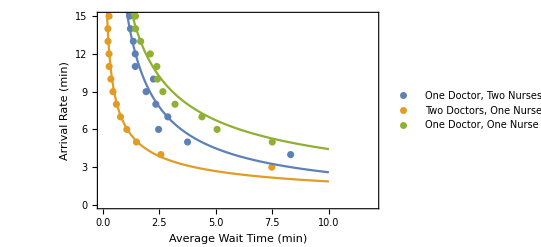

```mathematica
waitPlot = ListPlot[waitData, PlotLegends->{"One Doctor, Two Nurses","Two Doctors, One Nurse","One Doctor, One Nurse"},Frame->True,FrameLabel->{"Average Wait Time (min)","Arrival Rate (min)"}];
fits = Table[NonlinearModelFit[waitData[[i]],a x^b,{a,b},x],{i,1,Length[calcData]}];
fitPlot=Plot[{fits[[1]][i],fits[[2]][i],fits[[3]][i]},{i,0,10}];
Show[waitPlot,fitPlot]
```

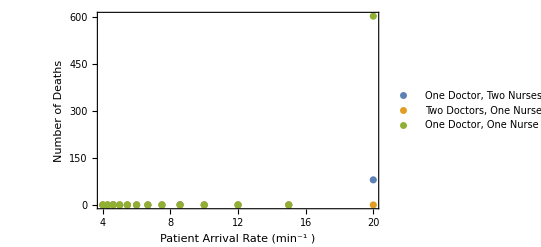

```mathematica
deathPlot = ListPlot[deathData,PlotLegends->{"One Doctor, Two Nurses","Two Doctors, One Nurse","One Doctor, One Nurse"},Frame->True,FrameLabel->{"Patient Arrival Rate (min^-1 )", "Number of Deaths"},PlotTheme->"Monochrome"]
```